#### 2D Harmonic Solution

```mathematica
θ[x_, y_, a_, b_, k_]:= k*Log10[Sqrt[(x- a)^2 + (y-b)^2]];
```

```mathematica
Subscript[n, 1][x_, y_, a_, b_, k_]:= Sin[θ[x, y, a, b, k]];
Subscript[n, 2][x_, y_, a_, b_, k_]:= Cos[θ[x, y, a, b, k]];
(*a = 0.5, b = -0.1, k = -4.5*)
```

```mathematica
Manipulate[VectorPlot[{Subscript[n, 1][x, y, a, b, k], Subscript[n, 2][x, y, a, b, k]}, {x, 0, 1}, {y, 0, 1}, VectorScale->0.05, VectorPoints->15], {a, -1, 1}, {b, -1, 1}, {k, -5, 5}]
```

```mathematica
Subscript[n, 1][0.51, 0.5, 0.5, 0.5, -3.0]
```

-0.279415

#### 3D Harmonic Solution

```mathematica
(*Stereographic Projection*)
Subscript[π, 0][{x_, y_, z_}] := {x/(1-z), y/(1-z)};
Subscript[π, 1][{x_, y_}]:={2x/(1+x^2+y^2), 2y/(1+x^2+y^2),(-1+x^2+y^2) /(1+x^2+y^2)}
```

```mathematica
Subscript[r, 1][{x_, y_}]:= {x/(x^2+ y^2) + x^2-y^2, 2x y-y/(x^2+y^2)}
(*Subscript[r, 1][{x_, y_}]:= {y^2- x^2, -2x y}*)
```

```mathematica
p[x_, y_, z_] := {x/Sqrt[x^2+y^2+z^2], y/Sqrt[x^2+y^2+z^2], z/Sqrt[x^2+y^2+z^2]}
```

```mathematica
n[x_, y_, z_]:= Subscript[π, 1][Subscript[r, 1][Subscript[π, 0][p[x+0.2, y+0.1, z]]]]
```

```mathematica
vis[δ_,r_,dx_,dy_, dz_]:=Graphics3D[Flatten[Table[Cylinder[{{x,y,z}-δ{n[x,y, z]⟦1⟧,n[x,y, z]⟦2⟧,n[x,y, z]⟦3⟧}/2,{x,y,z}+δ{n[x,y, z]⟦1⟧,n[x,y, z]⟦2⟧,n[x,y, z]⟦3⟧}/2},r],{x,0,1,dx},{y,0,1,dy}, {z, 0, 1, dz}]],PlotRange->All, Axes->{True, True, True}, BaseStyle->{FontSize->30}];
Show[vis[0.08,0.01,1/6,1/6, 1/6],ImageSize-> Large, LabelStyle-> {Black, Bold, FontFamily->"Helvetica",FontSize-> 26},AxesStyle->Thickness[0.003],Axes-> {True,True,True}, AxesLabel->{"X", "Y", "Z"},Boxed-> False, Ticks->{{{1.0, "1.0"}}, {{0.0, "0.0"}}, {{0.0, "0.0"}, {1.0, "1.0"} }}]
```

-Graphics3D-

```mathematica
(*Export["/Users/David/Desktop/ResearchRepos/AdaptiveRefinementResearch/RefinementPercentageNote/Figures/3DHolomorph1Cylinders.png",%12,  ImageResolution-> 300]*)
```

```mathematica
vis2D[δ_,r_,dx_,dy_]:=Graphics3D[Flatten[Table[Cylinder[{{x,y,0}-δ{n[x,y, 0.13]⟦1⟧,n[x,y, 0.13]⟦2⟧,n[x,y, 0.13]⟦3⟧}/2,{x,y,0}+δ{n[x,y, 0.13]⟦1⟧,n[x,y, 0.13]⟦2⟧,n[x,y, 0.13]⟦3⟧}/2},r],{x,0,1,dx},{y,0,1,dy}]],PlotRange->All, Axes->{True, True, False}, BaseStyle->{FontSize->30}];
Show[vis2D[0.05,0.01,1/13,1/13],ImageSize-> Large, LabelStyle-> {FontFamily->"Helvetica",FontSize-> 26},AxesStyle->Thickness[0.003],Axes-> {True,True,False},Boxed-> False,ViewPoint->{0,0,8},ViewVertical->{0,1,0}]
```

-Graphics3D-

```mathematica
(*Export["/Users/David/Desktop/ResearchRepos/AdaptiveRefinementResearch/RefinementPercentageNote/Figures/SliceHolomorph1Cylinders.png",%107,  ImageResolution-> 300]*)
```

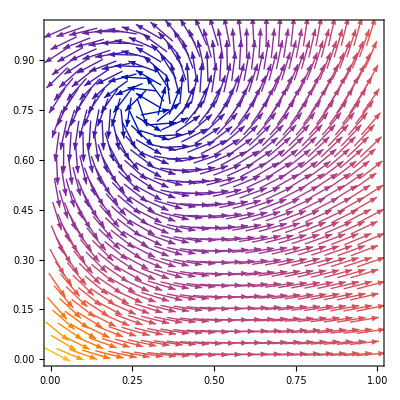

```mathematica
Subscript[r, 1][x_, y_]:= {x/(x^2+ y^2) + x^2-y^2, 2x y-y/(x^2+y^2)}
VectorPlot[{Subscript[r, 1][x+0.2, y+0.1]}, {x, 0, 1.0}, {y, 0, 1.0}, VectorScale->0.07, VectorPoints->25]
```

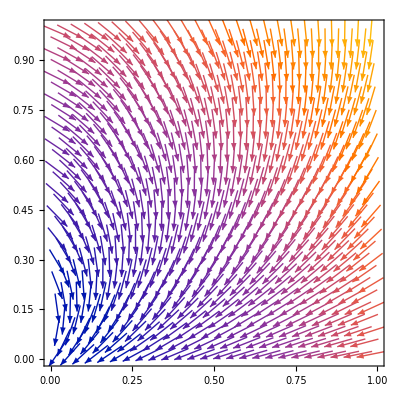

```mathematica
Subscript[r, 1][x_, y_]:= { -x^2+y^2,- 2x y}
VectorPlot[{Subscript[r, 1][x+0.2, y+0.1]}, {x, 0, 1.0}, {y, 0, 1.0}, VectorScale->0.07, VectorPoints->25]
```

#### Checking Unit Length Adherence

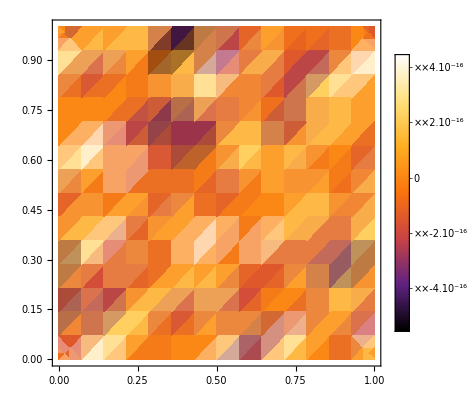

```mathematica
DensityPlot[(n[x,y,0.0].n[x,y,0.0]-1), {x, 0, 1}, {y, 0,1},ColorFunction->"SunsetColors", PlotLegends->Automatic]
```

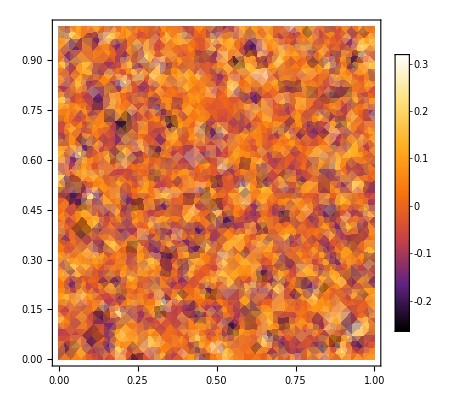

```mathematica
m = 0.1;
Subscript[γ, 1][x_, y_, z_]:=m*RandomReal[{-1,1}]
Subscript[γ, 2][x_, y_, z_]:=m*RandomReal[{-1,1}]
Subscript[γ, 3][x_, y_, z_]:=m*RandomReal[{-1,1}]
η[x_, y_, z_]:={n[x, y, z]⟦1⟧+Subscript[γ, 1][x, y, z],n[x, y, z] ⟦2⟧+Subscript[γ, 2][x, y,z], n[x, y, z]⟦3⟧+Subscript[γ, 3][x, y,z]}
DensityPlot[(η[x, y, 0.1]⟦1⟧)^2+(η[x, y, 0.1]⟦2⟧)^2+(η[x, y, 0.1]⟦3⟧)^2-1, {x, 0, 1}, {y, 0,1},ColorFunction->"SunsetColors", PlotLegends->Automatic]
```